```mathematica
mn = 0.939;

μ[mx_]:=mx/mn;
γ[ve_]:= 1/Sqrt[1 - ve^2]; (*natural units *)
p[ve_, mx_]:=γ[ve]*mx*ve*0.5;
s[mx_] :=(*2γ[0.6]*mx*mn+mx^2+mn^2;*)mx^2/μ[mx]^2*(1+μ[mx]^2+2/(√0.3)*μ[mx]);
Er[ctheta_,ve_, mx_]:= (mn*mx^2*γ[ve]^2*ve^2)/(mn^2 + mx^2 + 2*γ[ve]*mx*mn)*(1 - ctheta);
jacobian[B_, mx_]:=B*((1+μ[mx]^2+2/(√B)*μ[mx])/(2*(1-B)*mx^2));
```

```mathematica
σTot[dσ_, mx_]:= Integrate[dσ[t,mx] ,{t,(*-4 p[0.6, mx]^2*)-4*mx^2*((1-0.3)/(0.3*(1+μ[mx]^2+2/(√0.3)*μ[mx]))),0}]*jacobian[0.3, mx];
```

## Differential Cross Sections

```mathematica
d1[t_,mx_]:= (mn^2*(4*mx^2-t)*(4*mx^2-μ[mx]^2*t))/(32*π*(μ[mx]+1)^2*mx^2);
d2[t_, mx_]:= (mn^2*t*(μ[mx]^2*t - 4*mx^2))/(32*π*s[ mx]);
d3[t_, mx_]:= (mn^2*t*(t - 4*mx^2))/(32*π*s[ mx]);
d4[t_, mx_]:= (mn^2*t^2)/(32*π*s[mx]);
d5[t_,mx_]:= (2*(μ[mx]^2+1)^2*mx^4-4*(μ[mx]^2+1)*μ[mx]^2*s[ mx]*mx^2+μ[mx]^4*(2*s[ mx]^2+2*s[ mx]*t+t^2))/(16*π*μ[mx]^4*s[ mx]);
d6[t_, mx_]:= 1/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[mx] +s[ mx]+μ[mx]^2*t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[ mx]^2+2*s[ mx]*t+t^2));
d7[t_, mx_]:= 1/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[mx] +s[mx]+t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2));
```

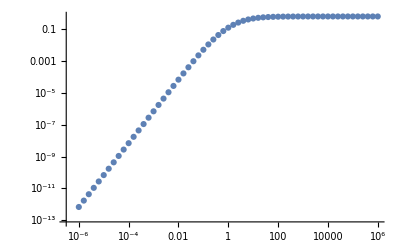

```mathematica
ListLogLogPlot[Evaluate@Table[ With[{x := 10^xp}, Table[{x,σTot[thing, x]}, {xp, -6, 6, 0.2}]], {thing, {d5}}]]
```

```mathematica
d1low[cθ_,w_, mx_]:= (mn^2*mx^2)/(2*π*(μ[mx]+1)^2);
d2low[cθ_,w_, mx_]:= (mn^2*μ[mx]^2)/(8*π*(μ[mx]+1)^2)*((1-cθ)*w^2*(2*mx^2)/(1+μ[mx])^2);
d3low[cθ_,w_, mx_]:= (mn^2*μ[mx]^2)/(8*π*(μ[mx]+1)^2)*((1-cθ)*w^2*(2*mx^2)/(1+μ[mx])^2);
d4low[cθ_,w_, mx_]:= (mn^2*μ[mx]^2)/(32*π*(μ[mx]+1)^2)*((1-cθ)*w^2*(2*mx^2)/(1+μ[mx])^2)^2;
d5low[cθ_,w_, mx_]:= mx^2/(2*π*(μ[mx]+1)^2);
```

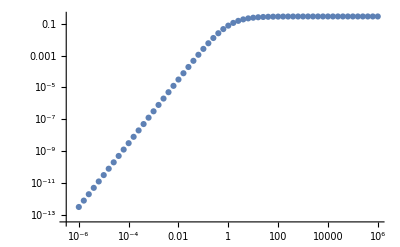

```mathematica
ListLogLogPlot[With[{x:=10^xp}, Table[{x, Integrate[d5low[y, 0.6, x], {y, -1,1}]}, {xp, -6, 6, 0.2}]]]
```

## Average over angles

```mathematica
avgθ[dσ_,mx_]:=Integrate[dσ[t,mx]*(-t)*(jacobian[0.3,mx])^2 ,{t,-4*mx^2*((1-0.3)/(0.3*(1+μ[mx]^2+2/(√0.3)*μ[mx]))),0}]/Integrate[dσ[t,mx]*jacobian[0.3, mx] ,{t,-4*mx^2*((1-0.3)/(0.3*(1+μ[mx]^2+2/(√0.3)*μ[mx]))),0}];
```

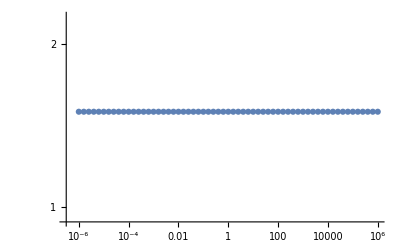

```mathematica
ListLogLogPlot[With[{x := 10^xp}, Table[{x,avgθ[d4, x]}, {xp, -6, 6, 0.2}]]]
```

```mathematica
qtr[dσ_, B_, mx_]:=√(2*mn*((1-B)*mx*μ[mx])/(B+2*√B*μ[mx]+B*μ[mx]^2)*avgθ[dσ, mx]);
```

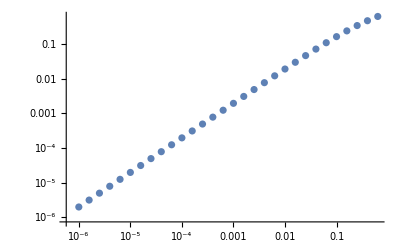

```mathematica
ListLogLogPlot[With[{x := 10^xp}, Table[{x,qtr[d5,0.3, x]}, {xp, -6, Log10[mn], 0.2}]]]
```